# Homework 8

-DeFilippis Jacob

## Question 1

```mathematica
Clear["Global`*"]
```

```mathematica
mandelbrot[cx_,cy_,lim_]:=Module[{z=0,ct=0},While[Abs[z]<2.0&&ct≤lim,z=z^2+cx+I cy;
++ct];
-ct];
```

```mathematica
mandelbrotC=Compile[{cx,cy,lim},Module[{z=0.+I 0.,ct=0},While[Abs[z]<2.0&&ct≤lim,z=z^2+cx+I cy;
++ct];
-ct]];
```

```mathematica
DensityPlot[mandelbrot[x,y,100],{x,-2,0.6},{y,-1.3,1.3},PlotPoints->200,Mesh->False,ColorFunction->(Hue[0.65 #1^0.6]&),FrameLabel->{"cx","cy"}]
```

-Graphics-

## Question 2

```mathematica
Clear["Global`*"]
```

```mathematica
r=26.5; σ = 10; b = 8/3;
```

```mathematica
sol = NDSolve[{x'[t]==σ (-x[t]+y[t]),y'[t]==-x[t] z[t]+r x[t]-y[t],z'[t]==x[t] y[t]- b z[t],x[0]==z[0]==0,y[0]==1},{x,y,z},{t,0,200},MaxSteps->Infinity]
```

{{x→InterpolatingFunction[{{0.,200.}},<>],y→InterpolatingFunction[{{0.,200.}},<>],z→InterpolatingFunction[{{0.,200.}},<>]}}

```mathematica
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.%],{t,0,200},PlotPoints->100000,ColorFunction->(ColorData["Rainbow"][#4]&)]
```

-Graphics3D-

```mathematica
xg=Plot[x[t]/. sol,{t,0,50},PlotStyle->{Red}];
yg=Plot[y[t]/. sol,{t,0,50},PlotStyle->{Blue}];
zg=Plot[z[t]/. sol,{t,0,50},PlotStyle->{Green}];
```

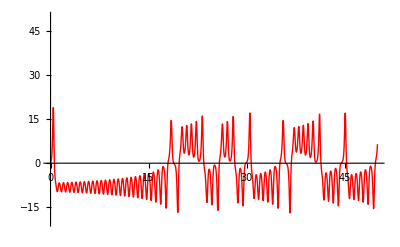

```mathematica
Show[xg,PlotRange->{-20,50}]
```

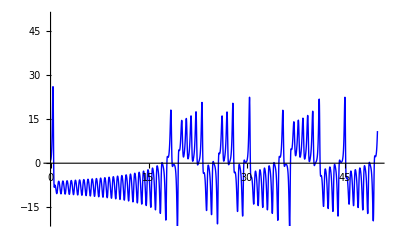

```mathematica
Show[yg,PlotRange->{-20,50}]
```

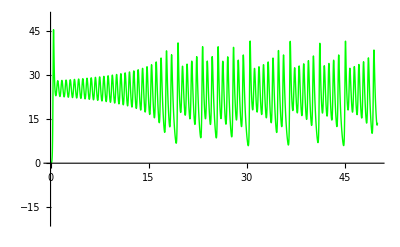

```mathematica
Show[zg,PlotRange->{-20,50}]
```

Looks pretty chaotic

## Question 3

```mathematica
Clear["Global`*"]
```

```mathematica
b=2.5; f =.8; a =.01;
```

```mathematica
sol1 = NDSolve[{ω'[t] == -Sin[θ[t]] - a ω[t]+f Cos[b t], θ'[t] == ω[t], θ[0]==0,ω[0]==0},{θ,ω},{t,0,100}];
```

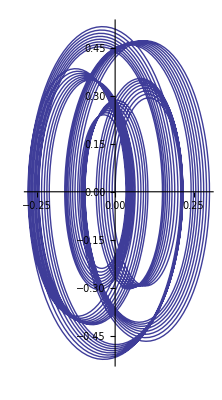

```mathematica
ParametricPlot[{θ[t],ω[t]}/.sol1,{t,0,100}]
```

```mathematica
poincare[b_,f_,a_,ndrop_,nplot_,psize_,pltr_]:=(T=2 π/b;g[{θold_,ωold_}]:={θ[T],ω[T]}/.NDSolve[{ω'[t] == -Sin[θ[t]] - a ω[t]+f Cos[b t], θ'[t] == ω[t], θ[0]==θold,ω[0]==ωold},{θ,ω},{t,0,T}][[1]];
lp=ListPlot[Drop[NestList[g,{0,0},nplot+ndrop],ndrop],PlotStyle->{PointSize[psize],Hue[0]},PlotRange->All,AxesLabel->{"θ","ω"}])
```

```mathematica
p1 =poincare[.3,.52,.2,500,5000,.02,.4];
```

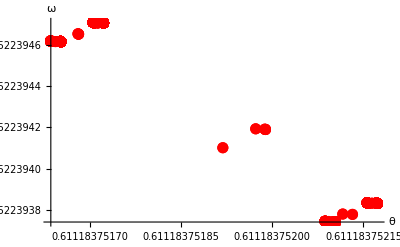

```mathematica
Show[p1,PlotRange->All]
```

This shows a more period pattern when the driving frequency is smaller

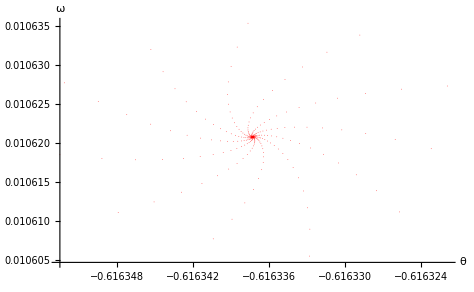

```mathematica
poincare[1.5,.8,.01,500,1000,.0002,.01]
```

And a more chaotic system when the driving frequency is high

## Question 4

## Part C

```mathematica
Clear["Global`*"]
```

```mathematica
f0=f;
```

```mathematica
f[n_]:=(4/3)^n
```

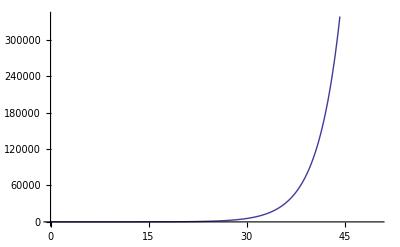

```mathematica
Plot[f[n],{n,0,50}]
```

Clearly the perimeter of the fractal approaches infinitely extremely fast when we iterate.

```mathematica
startlist1 = {{0,0},{3,0}};
startlist2 = {{3,0},{1.5,N[-3 Sqrt[3]/2]}};
startlist3 = {{1.5,N[ -3 Sqrt[3]/2]},{0,0}};
```

Part D

```mathematica
koch[{x_,y_}]:={{x,x+(y-x)/3},
{x+(y-x)/3,( y+x)/2 + N[(Sqrt[3]/2)]{(-1/3)(y-x)[[2]],(1/3)(y-x)[[1]]}},{( y+x)/2 +N[(Sqrt[3]/2)]{(-1/3)(y-x)[[2]],(1/3)(y-x)[[1]]},x+(2/3)(y-x)},{x+(2/3)(y-x),y}}
```

```mathematica
iterate[list_]:= Flatten[Map[koch,list],1]
```

```mathematica
newlist[n_]:= Nest[iterate,{startlist1,startlist2,startlist3},n];
```

```mathematica
snowflake[n_]:=Graphics[Line/@newlist[n]]
```

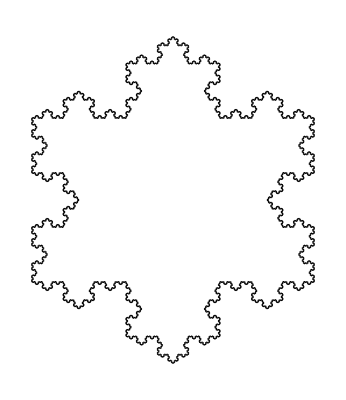

```mathematica
snowflake[5]
```

## Question 5

a) Potential

```mathematica
Clear["Global`*"]
```

```mathematica
L=1; Vo =25;
```

```mathematica
V[x_]:= -Vo/2 (1+Cos[2Pi x/L]) /; Abs[x] ≤ L/2
```

```mathematica
V[x_]:= 0 /; Abs[x] > L/2
```

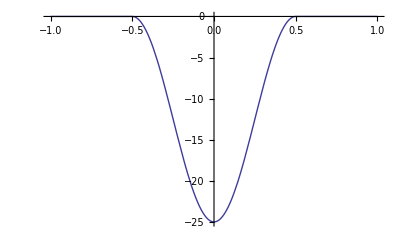

```mathematica
Plot[V[x],{x,-L,L}]
```

## b) EigenValue / Eigenfunction (Even)

```mathematica
B = 1;
ψ1[x_] := A Exp[ Abs[2 en]^(1/2) x]
ψ3[x_] := B Exp[- Abs[2 en]^(1/2) x]
```

```mathematica
eqn[en_] := ψ2''[x] + 2(en - V[x])ψ2[x]
```

```mathematica
wavefunc2[energy_] :=(en = energy; NDSolve[{ eqn[energy] == 0, ψ2[-L/2] ==  ψ1[-L/2], 
					ψ2'[-L/2] ==  ψ1'[-L/2]}, 
		ψ2, {x, -L/2, 0} ])
```

```mathematica
sol2[x_?NumericQ, en_?NumericQ] := ψ2[x] /. wavefunc2[en][[1]]
```

```mathematica
sol2prime[x_?NumericQ,en_?NumericQ]:=ψ2'[x]/.wavefunc2[en][[1]]
```

```mathematica
A=B;
```

```mathematica
eval = energy /. FindRoot [ sol2prime[0, energy],{energy, -5, -25} ]
```

-15.329

Energy ground state = -15.32

```mathematica
efunc2[x_]=ψ2[x]/.wavefunc2[eval][[1]];
```

```mathematica
ψnn [x_] := efunc2[-x] /; 0 ≤  x  ≤  L/2
```

```mathematica
ψnn[x_] := efunc2[x] /; -L/2 ≤  x  < 0
```

```mathematica
ψnn[x_] := ψ1[x] /; x < -L/2
```

```mathematica
ψnn [x_] := ψ3[x] /; x > L/2
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -Infinity, Infinity} ] ];
```

```mathematica
ψ[x_] := ψnn[x] / normconst;
```

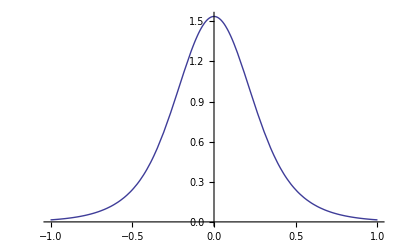

```mathematica
Plot[ψ[x],{x,-L,L}]
```

## c) EigenValue / Eigenfunction (Odd)

```mathematica
A=-B;
```

```mathematica
eval = en /. FindRoot [sol2[0, en] ,{en, -0.5, -25} ]
```

-0.92539

Energy  state of 1 = -.92

```mathematica
efunc2[x_]=ψ2[x]/.wavefunc2[eval][[1]];
```

```mathematica
ψnn [x_] := -efunc2[-x] /; 0 ≤  x  ≤  L/2
```

```mathematica
normconst = Sqrt[NIntegrate [ ψnn[x]^2, {x, -Infinity,Infinity} ] ];
```

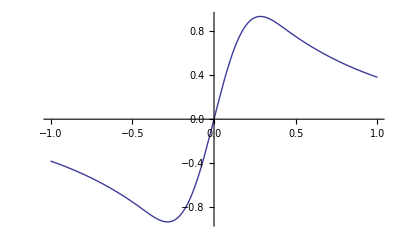

```mathematica
Plot[ψ[x],{x,-L,L}]
```

## d) Moar Bound States

```mathematica
Clear[A,B,eval]
```

```mathematica
Vo=250;B=1;A=B;
```

```mathematica
eval = energy /. FindRoot [ sol2prime[0, energy],{energy, -20, -50} ]
```

-92.5528

```mathematica
efunc2[x_]=ψ2[x]/.wavefunc2[eval][[1]];
```

```mathematica
ψnn [x_] := efunc2[-x] /; 0 ≤  x  ≤  L/2
```

```mathematica
ψnn[x_] := efunc2[x] /; -L/2 ≤  x  < 0
```

```mathematica
ψnn[x_] := ψ1[x] /; x < -L/2
```

```mathematica
ψnn [x_] := ψ3[x] /; x > L/2
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -Infinity, Infinity} ] ];
```

```mathematica
ψ[x_] := ψnn[x] / normconst;
```

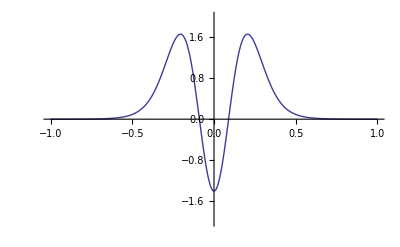

```mathematica
Plot[ψ[x],{x,-L,L},PlotRange->{-2,2}]
```

After a couple of attempts Vo around 150 gives even parity wavefunction (2 nodes) that is 6 x the original potential

## Question 6

```mathematica
Clear["Global`*"]
```

## Part A

```mathematica
L=20;
V[x_]:= -Sech[x]^2/; Abs[x]≤L/2
```

```mathematica
V[x_]:= 0/;Abs[x]>L/2
```

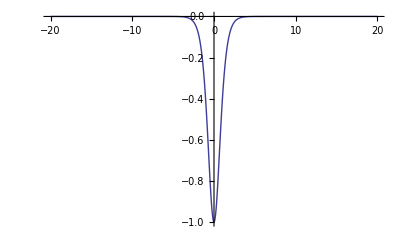

```mathematica
Plot[V[x],{x,-L,L},PlotRange->All]
```

```mathematica
Part B
```

B Part

```mathematica
B = 1;
ψ1[x_] := A Exp[ Abs[2 en]^(1/2) x]
ψ3[x_] := B Exp[- Abs[2 en]^(1/2) x]
```

```mathematica
eqn[en_] := ψ2''[x] + 2(en - V[x])ψ2[x]
```

```mathematica
wavefunc2[energy_] :=(en = energy; NDSolve[{ eqn[energy] == 0, ψ2[-L/2] ==  ψ1[-L/2], 
					ψ2'[-L/2] ==  ψ1'[-L/2]}, 
		ψ2, {x, -L/2, 0} ])
```

```mathematica
sol2[x_?NumericQ, en_?NumericQ] := ψ2[x] /. wavefunc2[en][[1]]
```

```mathematica
sol2prime[x_?NumericQ,en_?NumericQ]:=ψ2'[x]/.wavefunc2[en][[1]]
```

```mathematica
A=B;
```

```mathematica
eval = energy /. FindRoot [ sol2prime[0, energy],{energy, -1, 0} ]
```

-0.5

Energy ground state = -.5

```mathematica
efunc2[x_]=ψ2[x]/.wavefunc2[eval][[1]];
```

```mathematica
ψnn [x_] := efunc2[-x] /; 0 ≤  x  ≤  L/2
```

```mathematica
ψnn[x_] := efunc2[x] /; -L/2 ≤  x  < 0
```

```mathematica
ψnn[x_] := ψ1[x] /; x < -L/2
```

```mathematica
ψnn [x_] := ψ3[x] /; x > L/2
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -Infinity, Infinity} ] ];
```

```mathematica
ψ[x_] := ψnn[x] / normconst;
```

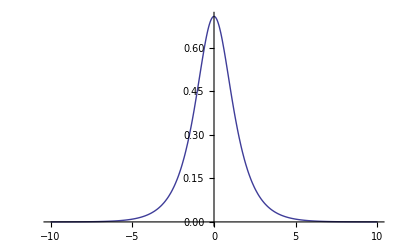

```mathematica
Plot[ψ[x],{x,-L/2,L/2},PlotRange->All]
```

```mathematica
Part C
```

C Part

```mathematica
ψknown[x_]:= (1/Sqrt[2])Sech[x]
```

```mathematica
V[x_]:= -Sech[x]^2
```

```mathematica
eqn[en_] := ψknown''[x] + 2(en - V[en])ψknown[x]
```

```mathematica
energy[x_]=Solve[eqn[en]==0,x][[1]];
```

```mathematica
en/.energy[0][[1]]
```

-0.5

Which is what we calculated before numerically

## Question 7

```mathematica
Clear["Global`*"]
```

```mathematica
V[x_] :=   .25x^4
```

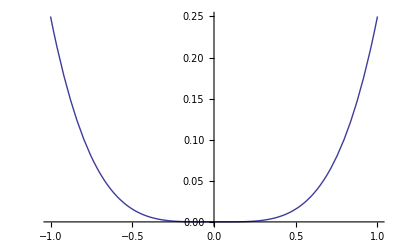

```mathematica
Plot[V[x], {x, -1, 1}]
```

```mathematica
L=4;
```

```mathematica
eqn[en_] := u''[x] + 2(en - V[x])u[x]
```

```mathematica
wavefunc[en_] := NDSolve[{ eqn[en] == 0, u[-L] ==  0, 
					u'[-L] == 1}, u, {x, -L, 0} ]
```

```mathematica
sol[x_?NumericQ, en_?NumericQ] := u[x] /.wavefunc[en][[1]]
```

```mathematica
solprime[x_?NumericQ, en_?NumericQ] := u'[x] /.wavefunc[en][[1]]
```

```mathematica
evalue = en /. FindRoot [  solprime[0, en] ,{en, 0, .5} ]
```

0.420805

```mathematica
efunc[x_] = u[x] /. wavefunc[evalue][[1]];
```

```mathematica
ψnn[x_] := efunc[x] /; x≤ 0 ;
```

```mathematica
ψnn [x_] := efunc[-x] /; x > 0 ;
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -L, L} ] ];
```

```mathematica
ψ[x_] := ψnn[x] / normconst;
```

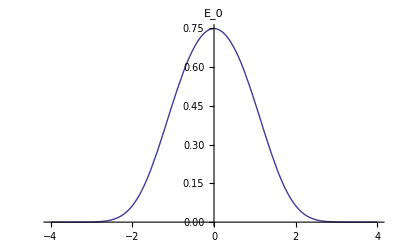

```mathematica
Plot[ψ[x],{x,-L,L},PlotLabel->"E_0"]
```

```mathematica
evalue = en /. FindRoot [  solprime[0, en] ,{en, 1, 1.9} ]
```

2.9588

```mathematica
efunc[x_] = u[x] /. wavefunc[evalue][[1]];
```

```mathematica
ψnn [x_] := -efunc[-x] /; x > 0
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -L, L} ] ];
```

```mathematica
ψ[x_] := ψnn[x] / normconst;
```

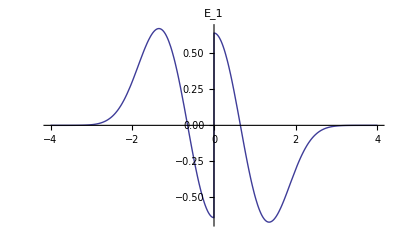

```mathematica
Plot[ψ[x],{x,-L,L},PlotLabel->"E_1"]
```

```mathematica
evalue = en /. FindRoot [  solprime[0, en] ,{en, 1.3, 3.5} ]
```

2.9588

```mathematica
efunc[x_] = u[x] /. wavefunc[evalue][[1]];
```

```mathematica
ψnn[x_] := efunc[x] /; x≤ 0 ;
```

```mathematica
ψnn [x_] := efunc[-x] /; x > 0 ;
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -L, L} ] ];
```

```mathematica
ψ[x_] := ψnn[x] / normconst;
```

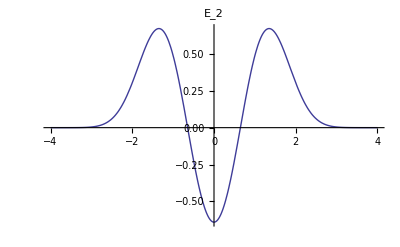

```mathematica
Plot[ψ[x],{x,-L,L},PlotLabel->"E_2"]
```